# Top

## Development Notebook

## Setup Packages

```mathematica
Needs["Ubuntu`Top`"];
```

```mathematica
Needs["Utilities`UnixTime`"];
```

```mathematica
Needs["Calendar`"];
```

```mathematica
Needs["Utilities`Debug`"]
```

http://linuxaria.com/howto/understanding-the-top-command-on-linux?lang=en

## MemoryQ and DurationQ

```mathematica
Map[Last[Quantity[1,#]]&,{"Bytes","Kilobytes","Megabytes","Gigabytes"}]
```

{Bytes,Kilobytes,Megabytes,Gigabytes}

```mathematica
Map[Last[Quantity[1,#]]&,{"Days","Hours","Minutes","Seconds"}]
```

{Days,Hours,Minutes,Seconds}

```mathematica
Map[MemoryQ[Quantity[1,#]]&,{"B","KB","MB","GB"}]//Tally
```

{{True,4}}

```mathematica
Map[MemoryQ[Quantity[1,#]]&,{"B","kB","mB","gB"}]
```

{True,True,True,True}

```mathematica
Map[DurationQ[Quantity[1,#]]&,{"d","h","min","s"}]
```

{True,True,True,True}

## Setup Data

```mathematica
dataDir=FileNameJoin[{ProjectDirectory["Ubuntu`Top`"],"TestData"}];
```

```mathematica
plotLabel="aws + ubuntu + node + haproxy + docker";
```

## TopDataFilePathQ

```mathematica
FileNames["top_*.txt",{dataDir}]
```

{/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt}

```mathematica
topDataFilePath=FileNames["top_*.txt",{dataDir}][[1]]
```

/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt

```mathematica
topDataFileTimestamp=TopDataFileTimestamp[topDataFilePath]
```

{2014,1,16,14,38,41.}

## TextFile

```mathematica
(*On[TextFile::import,TextFile::cache]*)
```

```mathematica
textFile=TextFile[topDataFilePath];
```

```mathematica
TextFileQ[textFile]//Timing
```

{0.00012,True}

```mathematica
FilePath[textFile]
```

/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt

```mathematica
FileDate[textFile]
```

{2014,1,17,9,31,16.}

```mathematica
FileByteCount[textFile]
```

6218702

```mathematica
FileHash[textFile]
```

30569810073339236264228381399421792778

```mathematica
Table[Timing[Length[Lines[textFile]]],{3}]//TableForm
```

1.81742 | 30512
0.01673 | 30512
0.00059 | 30512

```mathematica
Map[TextFileLineQ,Lines[textFile]]//Tally//Timing
```

{0.18067,{{True,30512}}}

```mathematica
Grid[Join[{{"LineNumber","LineText"}},Transpose[Map[Thread,Through[{LineNumber,LineText}[Lines[textFile][[;;10]]]]]]],Alignment->{{Right,Left},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

LineNumber | LineText
1 | top - 22:38:42 up 7 days, 23:33,  5 users,  load average: 1.28, 1.45, 1.34
2 | Tasks: 240 total,   1 running, 225 sleeping,   0 stopped,  14 zombie
3 | Cpu(s):  0.3%us,  0.2%sy,  0.0%ni, 99.4%id,  0.1%wa,  0.0%hi,  0.0%si,  0.0%st
4 | Mem:   7629464k total,  7296912k used,   332552k free,   414148k buffers
5 | Swap:        0k total,        0k used,        0k free,  5562092k cached
6 | 
7 |   PID USER      PR  NI  VIRT  RES  SHR S %CPU %MEM    TIME+  COMMAND                                                                                                                                            
8 | 14728 ubuntu    20   0 17472 1368  928 R    2  0.0   0:00.02 top                                                                                                                                                
9 |     1 root      20   0 24456 2424 1340 S    0  0.0   0:03.16 init                                                                                                                                               
10 |     2 root      20   0     0    0    0 S    0  0.0   0:00.03 kthreadd

```mathematica
SurroundingContext[Lines[textFile][[1]],1]
```

{TextFileLine[FilePath→/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt,LineNumber→2,LineText→Tasks: 240 total,   1 running, 225 sleeping,   0 stopped,  14 zombie]}

```mathematica
SurroundingContext[Lines[textFile][[10]],-1]
```

{TextFileLine[FilePath→/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt,LineNumber→9,LineText→    1 root      20   0 24456 2424 1340 S    0  0.0   0:03.16 init                                                                                                                                               ]}

## TopSummaryLine1

```mathematica
Lines[textFile][[1]]
```

TextFileLine[FilePath→/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt,LineNumber→1,LineText→top - 22:38:42 up 7 days, 23:33,  5 users,  load average: 1.28, 1.45, 1.34]

```mathematica
TopSummaryLine1[Lines[textFile][[1]]]
```

[top data]:top - 22:38:42 up 7 days, 23:33,  5 users,  load average: 1.28, 1.45, 1.34

```mathematica
Table[Timing[Length[Select[Lines[textFile],TopSummaryLine1SourceQ]]],{3}]//TableForm
```

0.43435 | 122
0.04585 | 122
0.05684 | 122

```mathematica
Table[Timing[Length[Map[TopSummaryLine1,Select[Lines[textFile],TopSummaryLine1SourceQ]]]],{3}]//TableForm
```

7.85156 | 122
0.05309 | 122
0.05527 | 122

```mathematica
topSummaryLine1List=Map[TopSummaryLine1,Select[Lines[textFile],TopSummaryLine1SourceQ]];
```

```mathematica
Grid[Join[{{"LineNumber","Timestamp","Uptime","UserSessions","LoadAverage1Minute","LoadAverage5Minute","LoadAverage15Minute"}},Transpose[Map[Thread,Through[{LineNumber,Timestamp,Uptime,UserSessions,LoadAverage1Minute,LoadAverage5Minute,LoadAverage15Minute}[topSummaryLine1List[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList],quantity_Quantity:>N[quantity]}],Alignment->{{Right,Left,Right,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

LineNumber | Timestamp | Uptime | UserSessions | LoadAverage1Minute | LoadAverage5Minute | LoadAverage15Minute
1 | Wed 1 Jan 2014 14:38:42 | 7.98125 | 5 | 1.28 | 1.45 | 1.34
250 | Wed 1 Jan 2014 14:38:45 | 7.98125 | 5 | 1.26 | 1.44 | 1.34
500 | Wed 1 Jan 2014 14:38:48 | 7.98125 | 5 | 1.26 | 1.44 | 1.34
749 | Wed 1 Jan 2014 14:38:51 | 7.98125 | 5 | 1.24 | 1.44 | 1.33
998 | Wed 1 Jan 2014 14:38:54 | 7.98125 | 5 | 1.22 | 1.43 | 1.33
1247 | Wed 1 Jan 2014 14:38:57 | 7.98125 | 5 | 1.22 | 1.43 | 1.33
1496 | Wed 1 Jan 2014 14:39:00 | 7.98125 | 5 | 1.2 | 1.42 | 1.33
1747 | Wed 1 Jan 2014 14:39:03 | 7.98125 | 5 | 1.2 | 1.42 | 1.33
1998 | Wed 1 Jan 2014 14:39:06 | 7.98125 | 5 | 1.18 | 1.41 | 1.33
2249 | Wed 1 Jan 2014 14:39:09 | 7.98125 | 5 | 1.17 | 1.41 | 1.33

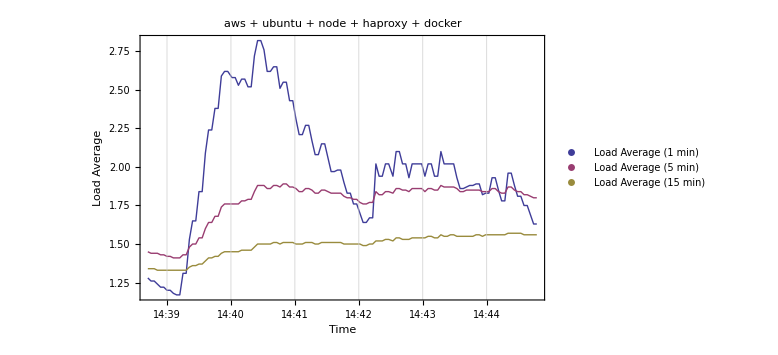

```mathematica
DateListPlot[Map[Transpose,Partition[Transpose[Transpose[Map[Thread,Through[{Timestamp,LoadAverage1Minute,LoadAverage5Minute,LoadAverage15Minute}[topSummaryLine1List]]]][[All,{1,2,1,3,1,4}]]],2]],PlotRange->All,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{"Time","Load Average"},PlotLabel->"aws + ubuntu + node + haproxy + docker",PlotLegends->{"Load Average (1 min)","Load Average (5 min)","Load Average (15 min)"},ImageSize->8 72]
```

```mathematica
Map[SetAttributes[#,Listable]&,{LineNumber,Timestamp,Uptime,UserSessions,LoadAverage1Minute,LoadAverage5Minute,LoadAverage15Minute}];
```

```mathematica
Map[ClearAttributes[#,Listable]&,{LineNumber,Timestamp,Uptime,UserSessions,LoadAverage1Minute,LoadAverage5Minute,LoadAverage15Minute}];
```

## TopSummaryLine2

```mathematica
Lines[textFile][[2]]
```

TextFileLine[FilePath→/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt,LineNumber→2,LineText→Tasks: 240 total,   1 running, 225 sleeping,   0 stopped,  14 zombie]

```mathematica
TopSummaryLine2[Lines[textFile][[2]]]
```

[top data]:Tasks: 240 total,   1 running, 225 sleeping,   0 stopped,  14 zombie

```mathematica
Table[Timing[Length[Select[Lines[textFile],TopSummaryLine2SourceQ]]],{3}]//TableForm
```

0.45554 | 122
0.04916 | 122
0.05547 | 122

```mathematica
Table[Timing[Length[Map[TopSummaryLine2,Select[Lines[textFile],TopSummaryLine2SourceQ]]]],{3}]//TableForm
```

0.06652 | 122
0.05562 | 122
0.05553 | 122

```mathematica
topSummaryLine2List=Map[TopSummaryLine2,Select[Lines[textFile],TopSummaryLine2SourceQ]];
```

```mathematica
Grid[Join[{{"LineNumber","TotalProcesses","TotalRunningProcesses","TotalSleepingProcesses","TotalStoppedProcesses","TotalZombieProcesses"}},Transpose[Map[Thread,Through[{LineNumber,TotalProcesses,TotalRunningProcesses,TotalSleepingProcesses,TotalStoppedProcesses,TotalZombieProcesses}[topSummaryLine2List[[;;10]]]]]]],Alignment->{{Right,Right,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

LineNumber | TotalProcesses | TotalRunningProcesses | TotalSleepingProcesses | TotalStoppedProcesses | TotalZombieProcesses
2 | 240 | 1 | 225 | 0 | 14
251 | 241 | 1 | 226 | 0 | 14
501 | 240 | 1 | 225 | 0 | 14
750 | 240 | 1 | 225 | 0 | 14
999 | 240 | 2 | 224 | 0 | 14
1248 | 240 | 1 | 225 | 0 | 14
1497 | 242 | 1 | 227 | 0 | 14
1748 | 242 | 1 | 227 | 0 | 14
1999 | 242 | 1 | 227 | 0 | 14
2250 | 242 | 1 | 227 | 0 | 14

## TopSummaryLine3

```mathematica
Lines[textFile][[3]]
```

TextFileLine[FilePath→/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt,LineNumber→3,LineText→Cpu(s):  0.3%us,  0.2%sy,  0.0%ni, 99.4%id,  0.1%wa,  0.0%hi,  0.0%si,  0.0%st]

```mathematica
TopSummaryLine3[Lines[textFile][[3]]]
```

[top data]:Cpu(s):  0.3%us,  0.2%sy,  0.0%ni, 99.4%id,  0.1%wa,  0.0%hi,  0.0%si,  0.0%st

```mathematica
Table[Timing[Length[Select[Lines[textFile],TopSummaryLine3SourceQ]]],{3}]//TableForm
```

0.45384 | 122
0.04621 | 122
0.05942 | 122

```mathematica
Table[Timing[Length[Map[TopSummaryLine3,Select[Lines[textFile],TopSummaryLine3SourceQ]]]],{3}]//TableForm
```

0.07683 | 122
0.05261 | 122
0.04527 | 122

```mathematica
topSummaryLine3List=Map[TopSummaryLine3,Select[Lines[textFile],TopSummaryLine3SourceQ]];
```

```mathematica
Grid[Join[{{"LineNumber","CPUPercentForUserProcesses","CPUPercentForSystemProcesses","CPUPercentWithPriorityUpgrade","CPUPercentNotUsed","CPUPercentForProcessesWaitingForIO","CPUPercentServingHardwareInterupts","CPUPercentServingSoftwareInterupts","CPUPercentStolenByHypervisor"}},Transpose[Map[Thread,Through[{LineNumber,CPUPercentForUserProcesses,CPUPercentForSystemProcesses,CPUPercentWithPriorityUpgrade,CPUPercentNotUsed,CPUPercentForProcessesWaitingForIO,CPUPercentServingHardwareInterupts,CPUPercentServingSoftwareInterupts,CPUPercentStolenByHypervisor}[topSummaryLine3List[[;;10]]]]]]],Alignment->{{Right,Right,Right,Right,Right,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

LineNumber | CPUPercentForUserProcesses | CPUPercentForSystemProcesses | CPUPercentWithPriorityUpgrade | CPUPercentNotUsed | CPUPercentForProcessesWaitingForIO | CPUPercentServingHardwareInterupts | CPUPercentServingSoftwareInterupts | CPUPercentStolenByHypervisor
3 | 0.3 | 0.2 | 0. | 99.4 | 0.1 | 0. | 0. | 0.
252 | 0.2 | 0.8 | 0. | 98.8 | 0.2 | 0. | 0. | 0.
502 | 0.2 | 0.3 | 0. | 99.5 | 0. | 0. | 0. | 0.
751 | 0.3 | 1.2 | 0. | 98.2 | 0.2 | 0. | 0. | 0.2
1000 | 0.3 | 0.5 | 0. | 99. | 0. | 0. | 0.2 | 0.
1249 | 0.3 | 0.5 | 0. | 99.2 | 0. | 0. | 0. | 0.
1498 | 0.7 | 1. | 0. | 98.3 | 0. | 0. | 0. | 0.
1749 | 0.2 | 0.5 | 0. | 99.3 | 0. | 0. | 0. | 0.
2000 | 0.2 | 0.7 | 0. | 99.2 | 0. | 0. | 0. | 0.
2251 | 0.3 | 0.5 | 0. | 99.2 | 0. | 0. | 0. | 0.

## TopSummaryLine4

```mathematica
Lines[textFile][[4]]
```

TextFileLine[FilePath→/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt,LineNumber→4,LineText→Mem:   7629464k total,  7296912k used,   332552k free,   414148k buffers]

```mathematica
TopSummaryLine4[Lines[textFile][[4]]]
```

[top data]:Mem:   7629464k total,  7296912k used,   332552k free,   414148k buffers

```mathematica
Table[Timing[Length[Select[Lines[textFile],TopSummaryLine4SourceQ]]],{3}]//TableForm
```

0.49925 | 122
0.0522 | 122
0.05105 | 122

```mathematica
Table[Timing[Length[Map[TopSummaryLine4,Select[Lines[textFile],TopSummaryLine4SourceQ]]]],{3}]//TableForm
```

0.07848 | 122
0.05204 | 122
0.04983 | 122

```mathematica
topSummaryLine4List=Map[TopSummaryLine4,Select[Lines[textFile],TopSummaryLine4SourceQ]];
```

```mathematica
Grid[Join[{{"LineNumber","TotalPhysicalMemory","UsedPhysicalMemory","FreePhysicalMemory","BufferPhysicalMemory"}},Transpose[Map[Thread,Through[{LineNumber,TotalPhysicalMemory,UsedPhysicalMemory,FreePhysicalMemory,BufferPhysicalMemory}[topSummaryLine4List[[;;10]]]]]]],Alignment->{{Right,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

LineNumber | TotalPhysicalMemory | UsedPhysicalMemory | FreePhysicalMemory | BufferPhysicalMemory
4 | 7629464 | 7296912 | 332552 | 414148
253 | 7629464 | 7295432 | 334032 | 414164
503 | 7629464 | 7294564 | 334900 | 414164
752 | 7629464 | 7293812 | 335652 | 414180
1001 | 7629464 | 7292572 | 336892 | 414180
1250 | 7629464 | 7292448 | 337016 | 414196
1499 | 7629464 | 7292836 | 336628 | 414196
1750 | 7629464 | 7292960 | 336504 | 414212
2001 | 7629464 | 7292960 | 336504 | 414212
2252 | 7629464 | 7292960 | 336504 | 414228

## TopSummaryLine5

```mathematica
Lines[textFile][[5]]
```

TextFileLine[FilePath→/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt,LineNumber→5,LineText→Swap:        0k total,        0k used,        0k free,  5562092k cached]

```mathematica
TopSummaryLine4[Lines[textFile][[5]]]
```

TopSummaryLine4[TextFileLine[FilePath→/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt,LineNumber→5,LineText→Swap:        0k total,        0k used,        0k free,  5562092k cached]]

```mathematica
Table[Timing[Length[Select[Lines[textFile],TopSummaryLine5SourceQ]]],{3}]//TableForm
```

0.43122 | 122
0.07817 | 122
0.05474 | 122

```mathematica
Table[Timing[Length[Map[TopSummaryLine5,Select[Lines[textFile],TopSummaryLine5SourceQ]]]],{3}]//TableForm
```

0.08559 | 122
0.05658 | 122
0.0441 | 122

```mathematica
topSummaryLine5List=Map[TopSummaryLine5,Select[Lines[textFile],TopSummaryLine5SourceQ]];
```

```mathematica
Grid[Join[{{"LineNumber","TotalSwapMemory","UsedSwapMemory","FreeSwapMemory","CachedSwapMemory"}},Transpose[Map[Thread,Through[{LineNumber,TotalSwapMemory,UsedSwapMemory,FreeSwapMemory,CachedSwapMemory}[topSummaryLine5List[[;;10]]]]]]],Alignment->{{Right,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

LineNumber | TotalSwapMemory | UsedSwapMemory | FreeSwapMemory | CachedSwapMemory
5 | 0 | 0 | 0 | 5562092
254 | 0 | 0 | 0 | 5562224
504 | 0 | 0 | 0 | 5562344
753 | 0 | 0 | 0 | 5562472
1002 | 0 | 0 | 0 | 5562588
1251 | 0 | 0 | 0 | 5562704
1500 | 0 | 0 | 0 | 5562844
1751 | 0 | 0 | 0 | 5562944
2002 | 0 | 0 | 0 | 5563080
2253 | 0 | 0 | 0 | 5563192

## TopSummary

```mathematica
Lines[textFile][[;;5]]
```

{TextFileLine[FilePath→/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt,LineNumber→1,LineText→top - 22:38:42 up 7 days, 23:33,  5 users,  load average: 1.28, 1.45, 1.34],TextFileLine[FilePath→/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt,LineNumber→2,LineText→Tasks: 240 total,   1 running, 225 sleeping,   0 stopped,  14 zombie],TextFileLine[FilePath→/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt,LineNumber→3,LineText→Cpu(s):  0.3%us,  0.2%sy,  0.0%ni, 99.4%id,  0.1%wa,  0.0%hi,  0.0%si,  0.0%st],TextFileLine[FilePath→/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt,LineNumber→4,LineText→Mem:   7629464k total,  7296912k used,   332552k free,   414148k buffers],TextFileLine[FilePath→/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt,LineNumber→5,LineText→Swap:        0k total,        0k used,        0k free,  5562092k cached]}

```mathematica
Transpose[{topSummaryLine1List,topSummaryLine2List,topSummaryLine3List,topSummaryLine4List,topSummaryLine5List}][[;;5]]
```

{{[top data]:top - 22:38:42 up 7 days, 23:33,  5 users,  load average: 1.28, 1.45, 1.34,[top data]:Tasks: 240 total,   1 running, 225 sleeping,   0 stopped,  14 zombie,[top data]:Cpu(s):  0.3%us,  0.2%sy,  0.0%ni, 99.4%id,  0.1%wa,  0.0%hi,  0.0%si,  0.0%st,[top data]:Mem:   7629464k total,  7296912k used,   332552k free,   414148k buffers,[top data]:Swap:        0k total,        0k used,        0k free,  5562092k cached},{[top data]:top - 22:38:45 up 7 days, 23:33,  5 users,  load average: 1.26, 1.44, 1.34,[top data]:Tasks: 241 total,   1 running, 226 sleeping,   0 stopped,  14 zombie,[top data]:Cpu(s):  0.2%us,  0.8%sy,  0.0%ni, 98.8%id,  0.2%wa,  0.0%hi,  0.0%si,  0.0%st,[top data]:Mem:   7629464k total,  7295432k used,   334032k free,   414164k buffers,[top data]:Swap:        0k total,        0k used,        0k free,  5562224k cached},{[top data]:top - 22:38:48 up 7 days, 23:33,  5 users,  load average: 1.26, 1.44, 1.34,[top data]:Tasks: 240 total,   1 running, 225 sleeping,   0 stopped,  14 zombie,[top data]:Cpu(s):  0.2%us,  0.3%sy,  0.0%ni, 99.5%id,  0.0%wa,  0.0%hi,  0.0%si,  0.0%st,[top data]:Mem:   7629464k total,  7294564k used,   334900k free,   414164k buffers,[top data]:Swap:        0k total,        0k used,        0k free,  5562344k cached},{[top data]:top - 22:38:51 up 7 days, 23:33,  5 users,  load average: 1.24, 1.44, 1.33,[top data]:Tasks: 240 total,   1 running, 225 sleeping,   0 stopped,  14 zombie,[top data]:Cpu(s):  0.3%us,  1.2%sy,  0.0%ni, 98.2%id,  0.2%wa,  0.0%hi,  0.0%si,  0.2%st,[top data]:Mem:   7629464k total,  7293812k used,   335652k free,   414180k buffers,[top data]:Swap:        0k total,        0k used,        0k free,  5562472k cached},{[top data]:top - 22:38:54 up 7 days, 23:33,  5 users,  load average: 1.22, 1.43, 1.33,[top data]:Tasks: 240 total,   2 running, 224 sleeping,   0 stopped,  14 zombie,[top data]:Cpu(s):  0.3%us,  0.5%sy,  0.0%ni, 99.0%id,  0.0%wa,  0.0%hi,  0.2%si,  0.0%st,[top data]:Mem:   7629464k total,  7292572k used,   336892k free,   414180k buffers,[top data]:Swap:        0k total,        0k used,        0k free,  5562588k cached}}

```mathematica
TopSummary[Sequence@@Transpose[{topSummaryLine1List,topSummaryLine2List,topSummaryLine3List,topSummaryLine4List,topSummaryLine5List}][[1]]]
```

[top data]:Wed 1 Jan 2014 14:38:42

```mathematica
Table[Timing[Length[Map[TopSummary@@#&,Transpose[{topSummaryLine1List,topSummaryLine2List,topSummaryLine3List,topSummaryLine4List,topSummaryLine5List}]]]],{3}]//TableForm
```

0.01294 | 122
0.00229 | 122
0.00172 | 122

```mathematica
topSummaryList=Map[TopSummary@@#&,Transpose[{topSummaryLine1List,topSummaryLine2List,topSummaryLine3List,topSummaryLine4List,topSummaryLine5List}]];
```

```mathematica
topSummaryList[[1]]
```

[top data]:Wed 1 Jan 2014 14:38:42

```mathematica
Grid[Join[{{"Timestamp","Uptime","UserSessions","LoadAverage1Minute","LoadAverage5Minute","LoadAverage15Minute"}},Transpose[Map[Thread,Through[{Timestamp,Uptime,UserSessions,LoadAverage1Minute,LoadAverage5Minute,LoadAverage15Minute}[topSummaryList[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList],quantity_Quantity:>N[quantity]}],Alignment->{{Right,Left,Right,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

Timestamp | Uptime | UserSessions | LoadAverage1Minute | LoadAverage5Minute | LoadAverage15Minute
Wed 1 Jan 2014 14:38:42 | 7.98125 | 5 | 1.28 | 1.45 | 1.34
Wed 1 Jan 2014 14:38:45 | 7.98125 | 5 | 1.26 | 1.44 | 1.34
Wed 1 Jan 2014 14:38:48 | 7.98125 | 5 | 1.26 | 1.44 | 1.34
Wed 1 Jan 2014 14:38:51 | 7.98125 | 5 | 1.24 | 1.44 | 1.33
Wed 1 Jan 2014 14:38:54 | 7.98125 | 5 | 1.22 | 1.43 | 1.33
Wed 1 Jan 2014 14:38:57 | 7.98125 | 5 | 1.22 | 1.43 | 1.33
Wed 1 Jan 2014 14:39:00 | 7.98125 | 5 | 1.2 | 1.42 | 1.33
Wed 1 Jan 2014 14:39:03 | 7.98125 | 5 | 1.2 | 1.42 | 1.33
Wed 1 Jan 2014 14:39:06 | 7.98125 | 5 | 1.18 | 1.41 | 1.33
Wed 1 Jan 2014 14:39:09 | 7.98125 | 5 | 1.17 | 1.41 | 1.33

```mathematica
DateListPlot[Map[Transpose,Partition[Transpose[Transpose[Map[Thread,Through[{Timestamp,LoadAverage1Minute,LoadAverage5Minute,LoadAverage15Minute}[topSummaryList]]]][[All,{1,2,1,3,1,4}]]],2]],PlotRange->All,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{"Time","Load Average"},PlotLabel->plotLabel,PlotLegends->{"Load Average (1 min)","Load Average (5 min)","Load Average (15 min)"},ImageSize->8 72]
```

-Graphics-

```mathematica
Grid[Join[{{"Timestamp","TotalProcesses","TotalRunningProcesses","TotalSleepingProcesses","TotalStoppedProcesses","TotalZombieProcesses"}},Transpose[Map[Thread,Through[{Timestamp,TotalProcesses,TotalRunningProcesses,TotalSleepingProcesses,TotalStoppedProcesses,TotalZombieProcesses}[topSummaryList[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList]}],Alignment->{{Left,Right,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

Timestamp | TotalProcesses | TotalRunningProcesses | TotalSleepingProcesses | TotalStoppedProcesses | TotalZombieProcesses
Wed 1 Jan 2014 14:38:42 | 240 | 1 | 225 | 0 | 14
Wed 1 Jan 2014 14:38:45 | 241 | 1 | 226 | 0 | 14
Wed 1 Jan 2014 14:38:48 | 240 | 1 | 225 | 0 | 14
Wed 1 Jan 2014 14:38:51 | 240 | 1 | 225 | 0 | 14
Wed 1 Jan 2014 14:38:54 | 240 | 2 | 224 | 0 | 14
Wed 1 Jan 2014 14:38:57 | 240 | 1 | 225 | 0 | 14
Wed 1 Jan 2014 14:39:00 | 242 | 1 | 227 | 0 | 14
Wed 1 Jan 2014 14:39:03 | 242 | 1 | 227 | 0 | 14
Wed 1 Jan 2014 14:39:06 | 242 | 1 | 227 | 0 | 14
Wed 1 Jan 2014 14:39:09 | 242 | 1 | 227 | 0 | 14

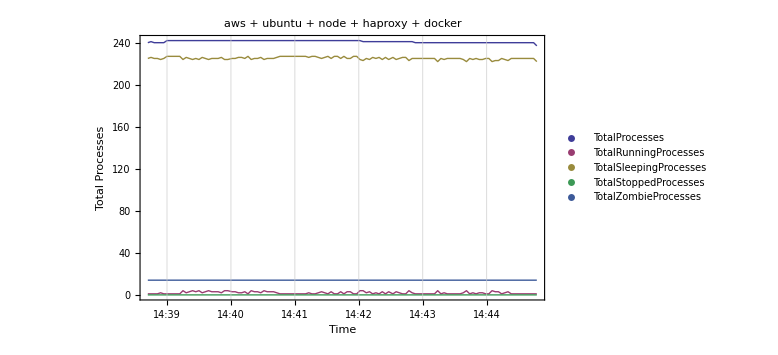

```mathematica
DateListPlot[Map[Transpose,Partition[Transpose[Transpose[Map[Thread,Through[{Timestamp,TotalProcesses,TotalRunningProcesses,TotalSleepingProcesses,TotalStoppedProcesses,TotalZombieProcesses}[topSummaryList]]]][[All,{1,2,1,3,1,4,1,5,1,6}]]],2]],PlotRange->All,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{"Time","Total Processes"},PlotLabel->plotLabel,PlotLegends->{"TotalProcesses","TotalRunningProcesses","TotalSleepingProcesses","TotalStoppedProcesses","TotalZombieProcesses"},ImageSize->8 72]
```

```mathematica
Grid[Join[{{"Timestamp","CPUPercentForUserProcesses","CPUPercentForSystemProcesses","CPUPercentWithPriorityUpgrade","CPUPercentNotUsed","CPUPercentForProcessesWaitingForIO","CPUPercentServingHardwareInterupts","CPUPercentServingSoftwareInterupts","CPUPercentStolenByHypervisor"}},Transpose[Map[Thread,Through[{Timestamp,CPUPercentForUserProcesses,CPUPercentForSystemProcesses,CPUPercentWithPriorityUpgrade,CPUPercentNotUsed,CPUPercentForProcessesWaitingForIO,CPUPercentServingHardwareInterupts,CPUPercentServingSoftwareInterupts,CPUPercentStolenByHypervisor}[topSummaryList[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList]}],Alignment->{{Left,Right,Right,Right,Right,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

Timestamp | CPUPercentForUserProcesses | CPUPercentForSystemProcesses | CPUPercentWithPriorityUpgrade | CPUPercentNotUsed | CPUPercentForProcessesWaitingForIO | CPUPercentServingHardwareInterupts | CPUPercentServingSoftwareInterupts | CPUPercentStolenByHypervisor
Wed 1 Jan 2014 14:38:42 | 0.3 | 0.2 | 0. | 99.4 | 0.1 | 0. | 0. | 0.
Wed 1 Jan 2014 14:38:45 | 0.2 | 0.8 | 0. | 98.8 | 0.2 | 0. | 0. | 0.
Wed 1 Jan 2014 14:38:48 | 0.2 | 0.3 | 0. | 99.5 | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 14:38:51 | 0.3 | 1.2 | 0. | 98.2 | 0.2 | 0. | 0. | 0.2
Wed 1 Jan 2014 14:38:54 | 0.3 | 0.5 | 0. | 99. | 0. | 0. | 0.2 | 0.
Wed 1 Jan 2014 14:38:57 | 0.3 | 0.5 | 0. | 99.2 | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 14:39:00 | 0.7 | 1. | 0. | 98.3 | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 14:39:03 | 0.2 | 0.5 | 0. | 99.3 | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 14:39:06 | 0.2 | 0.7 | 0. | 99.2 | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 14:39:09 | 0.3 | 0.5 | 0. | 99.2 | 0. | 0. | 0. | 0.

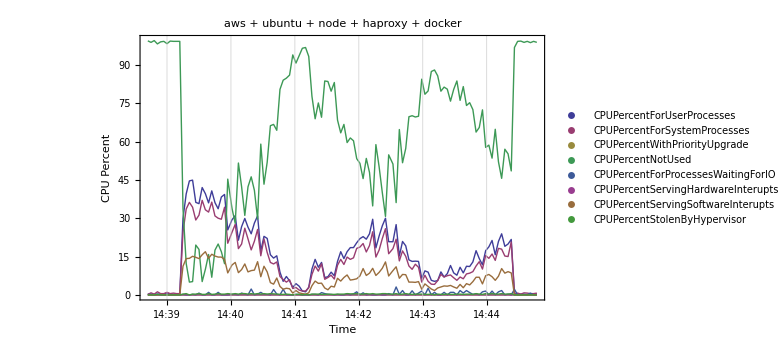

```mathematica
DateListPlot[Map[Transpose,Partition[Transpose[Transpose[Map[Thread,Through[{Timestamp,CPUPercentForUserProcesses,CPUPercentForSystemProcesses,CPUPercentWithPriorityUpgrade,CPUPercentNotUsed,CPUPercentForProcessesWaitingForIO,CPUPercentServingHardwareInterupts,CPUPercentServingSoftwareInterupts,CPUPercentStolenByHypervisor}[topSummaryList]]]][[All,{1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9}]]],2]],PlotRange->All,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{"Time","CPU Percent"},PlotLabel->plotLabel,PlotLegends->{"CPUPercentForUserProcesses","CPUPercentForSystemProcesses","CPUPercentWithPriorityUpgrade","CPUPercentNotUsed","CPUPercentForProcessesWaitingForIO","CPUPercentServingHardwareInterupts","CPUPercentServingSoftwareInterupts","CPUPercentStolenByHypervisor"},ImageSize->8 72]
```

```mathematica
Grid[Join[{{"Timestamp","TotalPhysicalMemory","UsedPhysicalMemory","FreePhysicalMemory","BufferPhysicalMemory"}},Transpose[Map[Thread,Through[{Timestamp,TotalPhysicalMemory,UsedPhysicalMemory,FreePhysicalMemory,BufferPhysicalMemory}[topSummaryList[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList]}],Alignment->{{Left,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

Timestamp | TotalPhysicalMemory | UsedPhysicalMemory | FreePhysicalMemory | BufferPhysicalMemory
Wed 1 Jan 2014 14:38:42 | 7629464 | 7296912 | 332552 | 414148
Wed 1 Jan 2014 14:38:45 | 7629464 | 7295432 | 334032 | 414164
Wed 1 Jan 2014 14:38:48 | 7629464 | 7294564 | 334900 | 414164
Wed 1 Jan 2014 14:38:51 | 7629464 | 7293812 | 335652 | 414180
Wed 1 Jan 2014 14:38:54 | 7629464 | 7292572 | 336892 | 414180
Wed 1 Jan 2014 14:38:57 | 7629464 | 7292448 | 337016 | 414196
Wed 1 Jan 2014 14:39:00 | 7629464 | 7292836 | 336628 | 414196
Wed 1 Jan 2014 14:39:03 | 7629464 | 7292960 | 336504 | 414212
Wed 1 Jan 2014 14:39:06 | 7629464 | 7292960 | 336504 | 414212
Wed 1 Jan 2014 14:39:09 | 7629464 | 7292960 | 336504 | 414228

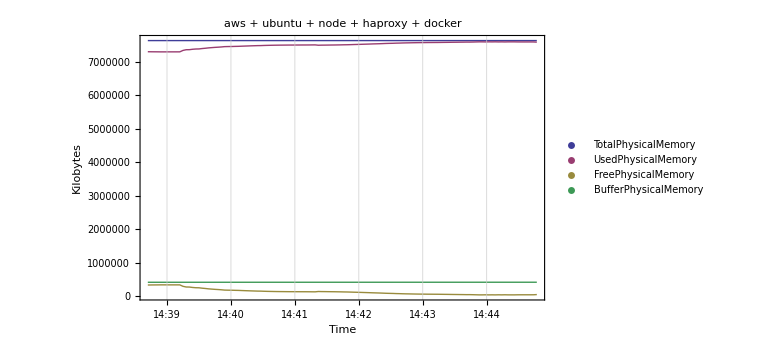

```mathematica
DateListPlot[Map[Transpose,Partition[Transpose[Transpose[Map[Thread,Through[{Timestamp,TotalPhysicalMemory,UsedPhysicalMemory,FreePhysicalMemory,BufferPhysicalMemory}[topSummaryList]]]][[All,{1,2,1,3,1,4,1,5}]]],2]],PlotRange->All,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{"Time","Kilobytes"},PlotLabel->plotLabel,PlotLegends->{"TotalPhysicalMemory","UsedPhysicalMemory","FreePhysicalMemory","BufferPhysicalMemory"},ImageSize->8 72]
```

```mathematica
Grid[Join[{{"Timestamp","TotalSwapMemory","UsedSwapMemory","FreeSwapMemory","CachedSwapMemory"}},Transpose[Map[Thread,Through[{Timestamp,TotalSwapMemory,UsedSwapMemory,FreeSwapMemory,CachedSwapMemory}[topSummaryList[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList]}],Alignment->{{Left,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

Timestamp | TotalSwapMemory | UsedSwapMemory | FreeSwapMemory | CachedSwapMemory
Wed 1 Jan 2014 14:38:42 | 0 | 0 | 0 | 5562092
Wed 1 Jan 2014 14:38:45 | 0 | 0 | 0 | 5562224
Wed 1 Jan 2014 14:38:48 | 0 | 0 | 0 | 5562344
Wed 1 Jan 2014 14:38:51 | 0 | 0 | 0 | 5562472
Wed 1 Jan 2014 14:38:54 | 0 | 0 | 0 | 5562588
Wed 1 Jan 2014 14:38:57 | 0 | 0 | 0 | 5562704
Wed 1 Jan 2014 14:39:00 | 0 | 0 | 0 | 5562844
Wed 1 Jan 2014 14:39:03 | 0 | 0 | 0 | 5562944
Wed 1 Jan 2014 14:39:06 | 0 | 0 | 0 | 5563080
Wed 1 Jan 2014 14:39:09 | 0 | 0 | 0 | 5563192

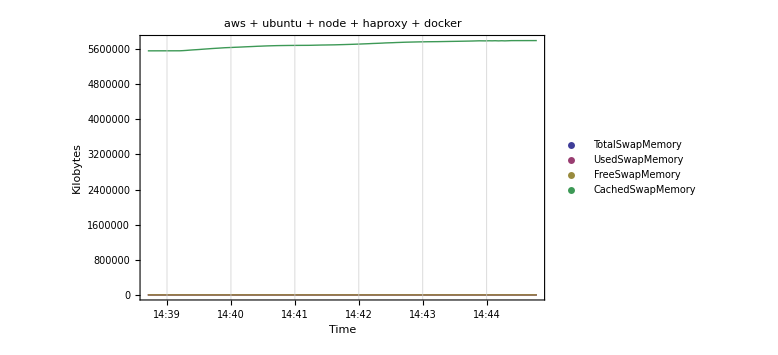

```mathematica
DateListPlot[Map[Transpose,Partition[Transpose[Transpose[Map[Thread,Through[{Timestamp,TotalSwapMemory,UsedSwapMemory,FreeSwapMemory,CachedSwapMemory}[topSummaryList]]]][[All,{1,2,1,3,1,4,1,5}]]],2]],PlotRange->All,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{"Time","Kilobytes"},PlotLabel->plotLabel,PlotLegends->{"TotalSwapMemory","UsedSwapMemory","FreeSwapMemory","CachedSwapMemory"},ImageSize->8 72]
```

## ProcessListItem

```mathematica
Table[Timing[Length[Select[Lines[textFile],ProcessListItemSourceQ]]],{3}]//TableForm
```

0.59753 | 29416
0.05547 | 29416
0.05525 | 29416

```mathematica
Table[Timing[Length[Map[ProcessListItem,Select[Lines[textFile],ProcessListItemSourceQ]]]],{3}]//TableForm
```

0.0945 | 29416
0.08572 | 29416
0.09343 | 29416

## TopLogFileData

```mathematica
topLogFileData=TopLogFileData[textFile];
```

```mathematica
TopLogFileDataQ[topLogFileData]//Timing
```

{0.00003,True}

```mathematica
FilePath[topLogFileData]
```

/Users/matt/WolframWorkspaces/Base/Ubuntu/TestData/top_1389911921.txt

```mathematica
Table[Timing[Length[Lines[topLogFileData]]],{3}]//TableForm
```

52.89286 | 122
0.39589 | 122
0.00007 | 122

```mathematica
Map[TopDataQ,Lines[topLogFileData]]//Tally//Timing
```

{0.00176,{{True,122}}}

```mathematica
Table[Timing[Length[Map[TopSummary,Lines[topLogFileData]]]],{3}]//TableForm
```

0.6582 | 122
0.82631 | 122
0.80481 | 122

```mathematica
topSummaryList=Map[TopSummary,Lines[topLogFileData]];
```

```mathematica
topSummaryList[[1]]
```

[top data]:Wed 1 Jan 2014 14:38:42

```mathematica
Grid[Join[{{"Timestamp","Uptime","UserSessions","LoadAverage1Minute","LoadAverage5Minute","LoadAverage15Minute"}},Transpose[Map[Thread,Through[{Timestamp,Uptime,UserSessions,LoadAverage1Minute,LoadAverage5Minute,LoadAverage15Minute}[topSummaryList[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList],quantity_Quantity:>N[quantity]}],Alignment->{{Right,Left,Right,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

Timestamp | Uptime | UserSessions | LoadAverage1Minute | LoadAverage5Minute | LoadAverage15Minute
Wed 1 Jan 2014 14:38:42 | 7.98125 | 5 | 1.28 | 1.45 | 1.34
Wed 1 Jan 2014 14:38:45 | 7.98125 | 5 | 1.26 | 1.44 | 1.34
Wed 1 Jan 2014 14:38:48 | 7.98125 | 5 | 1.26 | 1.44 | 1.34
Wed 1 Jan 2014 14:38:51 | 7.98125 | 5 | 1.24 | 1.44 | 1.33
Wed 1 Jan 2014 14:38:54 | 7.98125 | 5 | 1.22 | 1.43 | 1.33
Wed 1 Jan 2014 14:38:57 | 7.98125 | 5 | 1.22 | 1.43 | 1.33
Wed 1 Jan 2014 14:39:00 | 7.98125 | 5 | 1.2 | 1.42 | 1.33
Wed 1 Jan 2014 14:39:03 | 7.98125 | 5 | 1.2 | 1.42 | 1.33
Wed 1 Jan 2014 14:39:06 | 7.98125 | 5 | 1.18 | 1.41 | 1.33
Wed 1 Jan 2014 14:39:09 | 7.98125 | 5 | 1.17 | 1.41 | 1.33

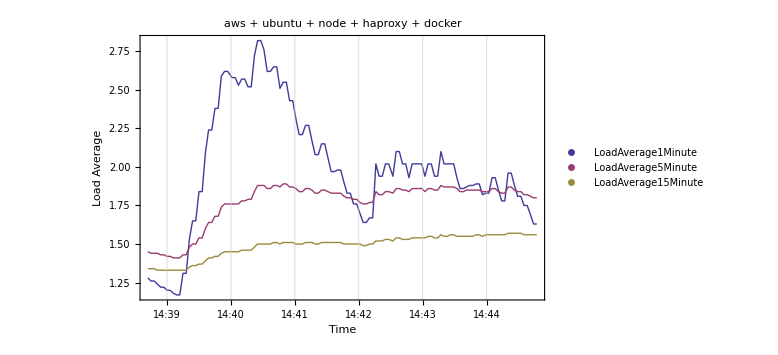

```mathematica
LoadAveragePlot[topLogFileData,plotLabel]
```

```mathematica
Grid[Join[{{"Timestamp","TotalProcesses","TotalRunningProcesses","TotalSleepingProcesses","TotalStoppedProcesses","TotalZombieProcesses"}},Transpose[Map[Thread,Through[{Timestamp,TotalProcesses,TotalRunningProcesses,TotalSleepingProcesses,TotalStoppedProcesses,TotalZombieProcesses}[topSummaryList[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList]}],Alignment->{{Left,Right,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

Timestamp | TotalProcesses | TotalRunningProcesses | TotalSleepingProcesses | TotalStoppedProcesses | TotalZombieProcesses
Wed 1 Jan 2014 14:38:42 | 240 | 1 | 225 | 0 | 14
Wed 1 Jan 2014 14:38:45 | 241 | 1 | 226 | 0 | 14
Wed 1 Jan 2014 14:38:48 | 240 | 1 | 225 | 0 | 14
Wed 1 Jan 2014 14:38:51 | 240 | 1 | 225 | 0 | 14
Wed 1 Jan 2014 14:38:54 | 240 | 2 | 224 | 0 | 14
Wed 1 Jan 2014 14:38:57 | 240 | 1 | 225 | 0 | 14
Wed 1 Jan 2014 14:39:00 | 242 | 1 | 227 | 0 | 14
Wed 1 Jan 2014 14:39:03 | 242 | 1 | 227 | 0 | 14
Wed 1 Jan 2014 14:39:06 | 242 | 1 | 227 | 0 | 14
Wed 1 Jan 2014 14:39:09 | 242 | 1 | 227 | 0 | 14

```mathematica
TotalProcessesPlot[topLogFileData,plotLabel]
```

-Graphics-

```mathematica
Grid[Join[{{"Timestamp","CPUPercentForUserProcesses","CPUPercentForSystemProcesses","CPUPercentWithPriorityUpgrade","CPUPercentNotUsed","CPUPercentForProcessesWaitingForIO","CPUPercentServingHardwareInterupts","CPUPercentServingSoftwareInterupts","CPUPercentStolenByHypervisor"}},Transpose[Map[Thread,Through[{Timestamp,CPUPercentForUserProcesses,CPUPercentForSystemProcesses,CPUPercentWithPriorityUpgrade,CPUPercentNotUsed,CPUPercentForProcessesWaitingForIO,CPUPercentServingHardwareInterupts,CPUPercentServingSoftwareInterupts,CPUPercentStolenByHypervisor}[topSummaryList[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList]}],Alignment->{{Left,Right,Right,Right,Right,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

Timestamp | CPUPercentForUserProcesses | CPUPercentForSystemProcesses | CPUPercentWithPriorityUpgrade | CPUPercentNotUsed | CPUPercentForProcessesWaitingForIO | CPUPercentServingHardwareInterupts | CPUPercentServingSoftwareInterupts | CPUPercentStolenByHypervisor
Wed 1 Jan 2014 14:38:42 | 0.3 | 0.2 | 0. | 99.4 | 0.1 | 0. | 0. | 0.
Wed 1 Jan 2014 14:38:45 | 0.2 | 0.8 | 0. | 98.8 | 0.2 | 0. | 0. | 0.
Wed 1 Jan 2014 14:38:48 | 0.2 | 0.3 | 0. | 99.5 | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 14:38:51 | 0.3 | 1.2 | 0. | 98.2 | 0.2 | 0. | 0. | 0.2
Wed 1 Jan 2014 14:38:54 | 0.3 | 0.5 | 0. | 99. | 0. | 0. | 0.2 | 0.
Wed 1 Jan 2014 14:38:57 | 0.3 | 0.5 | 0. | 99.2 | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 14:39:00 | 0.7 | 1. | 0. | 98.3 | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 14:39:03 | 0.2 | 0.5 | 0. | 99.3 | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 14:39:06 | 0.2 | 0.7 | 0. | 99.2 | 0. | 0. | 0. | 0.
Wed 1 Jan 2014 14:39:09 | 0.3 | 0.5 | 0. | 99.2 | 0. | 0. | 0. | 0.

```mathematica
CPUPercentPlot[topLogFileData,plotLabel]
```

-Graphics-

```mathematica
Grid[Join[{{"Timestamp","TotalPhysicalMemory","UsedPhysicalMemory","FreePhysicalMemory","BufferPhysicalMemory"}},Transpose[Map[Thread,Through[{Timestamp,TotalPhysicalMemory,UsedPhysicalMemory,FreePhysicalMemory,BufferPhysicalMemory}[topSummaryList[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList]}],Alignment->{{Left,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

Timestamp | TotalPhysicalMemory | UsedPhysicalMemory | FreePhysicalMemory | BufferPhysicalMemory
Wed 1 Jan 2014 14:38:42 | 7629464 | 7296912 | 332552 | 414148
Wed 1 Jan 2014 14:38:45 | 7629464 | 7295432 | 334032 | 414164
Wed 1 Jan 2014 14:38:48 | 7629464 | 7294564 | 334900 | 414164
Wed 1 Jan 2014 14:38:51 | 7629464 | 7293812 | 335652 | 414180
Wed 1 Jan 2014 14:38:54 | 7629464 | 7292572 | 336892 | 414180
Wed 1 Jan 2014 14:38:57 | 7629464 | 7292448 | 337016 | 414196
Wed 1 Jan 2014 14:39:00 | 7629464 | 7292836 | 336628 | 414196
Wed 1 Jan 2014 14:39:03 | 7629464 | 7292960 | 336504 | 414212
Wed 1 Jan 2014 14:39:06 | 7629464 | 7292960 | 336504 | 414212
Wed 1 Jan 2014 14:39:09 | 7629464 | 7292960 | 336504 | 414228

```mathematica
PhysicalMemoryPlot[topLogFileData,plotLabel]
```

-Graphics-

```mathematica
Grid[Join[{{"Timestamp","TotalSwapMemory","UsedSwapMemory","FreeSwapMemory","CachedSwapMemory"}},Transpose[Map[Thread,Through[{Timestamp,TotalSwapMemory,UsedSwapMemory,FreeSwapMemory,CachedSwapMemory}[topSummaryList[[;;10]]]]]]/.{dateList:_?DateQ:>DateString[dateList]}],Alignment->{{Left,Right,Right,Right,Right},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

Timestamp | TotalSwapMemory | UsedSwapMemory | FreeSwapMemory | CachedSwapMemory
Wed 1 Jan 2014 14:38:42 | 0 | 0 | 0 | 5562092
Wed 1 Jan 2014 14:38:45 | 0 | 0 | 0 | 5562224
Wed 1 Jan 2014 14:38:48 | 0 | 0 | 0 | 5562344
Wed 1 Jan 2014 14:38:51 | 0 | 0 | 0 | 5562472
Wed 1 Jan 2014 14:38:54 | 0 | 0 | 0 | 5562588
Wed 1 Jan 2014 14:38:57 | 0 | 0 | 0 | 5562704
Wed 1 Jan 2014 14:39:00 | 0 | 0 | 0 | 5562844
Wed 1 Jan 2014 14:39:03 | 0 | 0 | 0 | 5562944
Wed 1 Jan 2014 14:39:06 | 0 | 0 | 0 | 5563080
Wed 1 Jan 2014 14:39:09 | 0 | 0 | 0 | 5563192

```mathematica
SwapMemoryPlot[topLogFileData,plotLabel]
```

-Graphics-

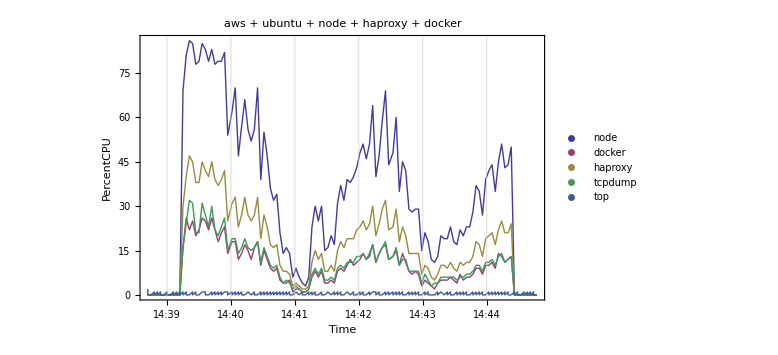

```mathematica
percentCPUPlot=CommandPlot[topLogFileData,plotLabel,{"node","docker","haproxy","tcpdump","top"},PercentCPU]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop",FileBaseName[topDataFilePath]<>"_percentCPUPlot"<>".png"}],percentCPUPlot]
```

/Users/matt/Desktop/top_1389911921_percentCPUPlot.png

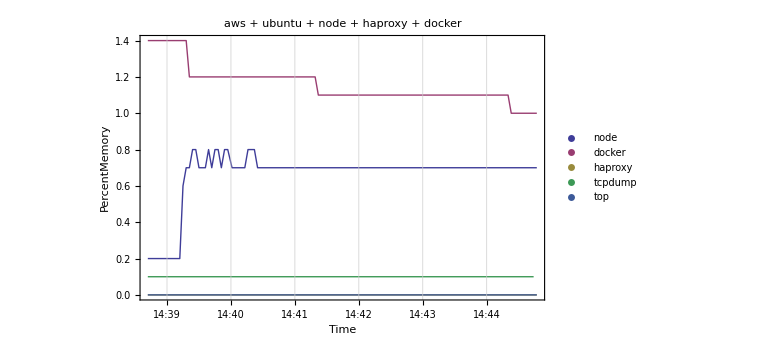

```mathematica
percentMemoryPlot=CommandPlot[topLogFileData,plotLabel,{"node","docker","haproxy","tcpdump","top"},PercentMemory]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop",FileBaseName[topDataFilePath]<>"_percentMemoryPlot"<>".png"}],percentMemoryPlot]
```

/Users/matt/Desktop/top_1389911921_percentMemoryPlot.png

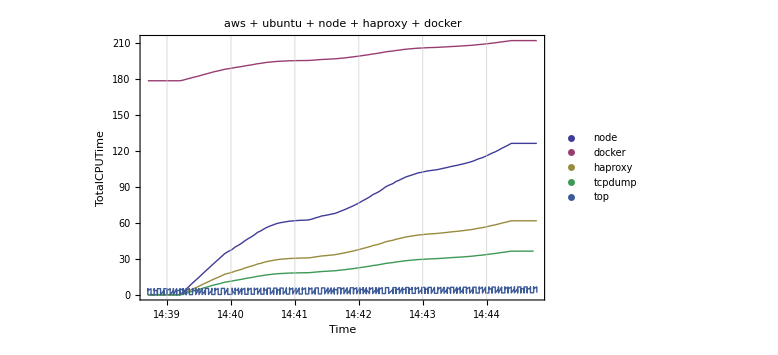

```mathematica
totalCPUTimePlot=CommandPlot[topLogFileData,plotLabel,{"node","docker","haproxy","tcpdump","top"},TotalCPUTime]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop",FileBaseName[topDataFilePath]<>"_totalCPUTimePlot"<>".png"}],totalCPUTimePlot]
```

/Users/matt/Desktop/top_1389911921_totalCPUTimePlot.png

```mathematica
Reverse[SortBy[Flatten[Map[ProcessListItemList,Lines[topLogFileData]]],PercentCPU]][[;;10]]//TableForm
```

[top data]:14673 root      20   0  656m  54m 5492 R   86  0.7   0:07.35 node                                                                                                                                               
[top data]:14673 root      20   0  657m  56m 5492 R   85  0.8   0:09.91 node                                                                                                                                               
[top data]:14673 root      20   0  656m  54m 5492 R   85  0.7   0:17.23 node                                                                                                                                               
[top data]:14673 root      20   0  656m  55m 5492 R   83  0.7   0:24.64 node                                                                                                                                               
[top data]:14673 root      20   0  656m  54m 5492 R   83  0.7   0:19.74 node                                                                                                                                               
[top data]:14673 root      20   0  658m  56m 5492 R   82  0.8   0:34.29 node                                                                                                                                               
[top data]:14673 root      20   0  655m  54m 5492 R   81  0.7   0:04.75 node                                                                                                                                               
[top data]:14673 root      20   0  657m  56m 5492 R   79  0.8   0:22.13 node                                                                                                                                               
[top data]:14673 root      20   0  657m  55m 5492 R   79  0.8   0:29.42 node                                                                                                                                               
[top data]:14673 root      20   0  657m  55m 5492 R   79  0.7   0:31.82 node

```mathematica
Reverse[SortBy[Select[Flatten[Map[ProcessListItemList,Lines[topLogFileData]]],!MemberQ[{"node","docker","haproxy","tcpdump","top"},Command[#]]&],PercentCPU]][[;;10]]//TableForm
```

[top data]:13277 ubuntu    20   0 25864 8432 1748 S    1  0.1   0:00.55 bash                                                                                                                                               
[top data]: 6440 ubuntu    20   0 27376 2684 1208 S    1  0.0   0:19.22 tmux                                                                                                                                               
[top data]: 6440 ubuntu    20   0 27376 2684 1208 S    1  0.0   0:19.10 tmux                                                                                                                                               
[top data]: 6440 ubuntu    20   0 27376 2680 1208 S    1  0.0   0:19.02 tmux                                                                                                                                               
[top data]: 6440 ubuntu    20   0 27376 2680 1208 S    1  0.0   0:18.74 tmux                                                                                                                                               
[top data]: 6440 ubuntu    20   0 27376 2680 1208 S    1  0.0   0:18.64 tmux                                                                                                                                               
[top data]:  671 syslog    20   0  247m 2540 1080 S    1  0.0   1:11.29 rsyslogd                                                                                                                                           
[top data]:14739 ubuntu    20   0  5884  676  568 S    0  0.0   0:00.02 tee                                                                                                                                                
[top data]:14739 ubuntu    20   0  5884  676  568 S    0  0.0   0:00.02 tee                                                                                                                                                
[top data]:14739 ubuntu    20   0  5884  676  568 S    0  0.0   0:00.02 tee

```mathematica
Grid[Join[{{"LineNumber","Timestamp","PID","User","Priority","Nice","VirtualMemory","PhysicalMemory","SharedMemory","Status","PercentCPU","PercentMemory","TotalCPUTime","Command"}},Transpose[Map[Thread,Through[{LineNumber,Timestamp,PID,User,Priority,Nice,VirtualMemory,PhysicalMemory,SharedMemory,Status,PercentCPU,PercentMemory,TotalCPUTime,Command}[FindProcessByCommand["node",topLogFileData]]]]]/.{dateList:_?DateQ:>DateString[dateList],quantity_Quantity:>N[quantity]}],Alignment->{{Right,Left,Right,Left,Right,Right,Right,Right,Right,Center,Right,Right,Right,Left},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

LineNumber | Timestamp | PID | User | Priority | Nice | VirtualMemory | PhysicalMemory | SharedMemory | Status | PercentCPU | PercentMemory | TotalCPUTime | Command
241 | Wed 1 Jan 2014 14:38:42 | 14673 | root | 20 | 0 | 6.44×10^8 | 1.4×10^7 | 5328. | S | 0 | 0.2 | 0.22 | node
490 | Wed 1 Jan 2014 14:38:45 | 14673 | root | 20 | 0 | 6.44×10^8 | 1.4×10^7 | 5328. | S | 0 | 0.2 | 0.22 | node
740 | Wed 1 Jan 2014 14:38:48 | 14673 | root | 20 | 0 | 6.44×10^8 | 1.4×10^7 | 5328. | S | 0 | 0.2 | 0.22 | node
989 | Wed 1 Jan 2014 14:38:51 | 14673 | root | 20 | 0 | 6.44×10^8 | 1.4×10^7 | 5328. | S | 0 | 0.2 | 0.22 | node
1238 | Wed 1 Jan 2014 14:38:54 | 14673 | root | 20 | 0 | 6.44×10^8 | 1.4×10^7 | 5328. | S | 0 | 0.2 | 0.22 | node
1488 | Wed 1 Jan 2014 14:38:57 | 14673 | root | 20 | 0 | 6.44×10^8 | 1.4×10^7 | 5328. | S | 0 | 0.2 | 0.22 | node
1736 | Wed 1 Jan 2014 14:39:00 | 14673 | root | 20 | 0 | 6.44×10^8 | 1.4×10^7 | 5328. | S | 0 | 0.2 | 0.22 | node
1987 | Wed 1 Jan 2014 14:39:03 | 14673 | root | 20 | 0 | 6.44×10^8 | 1.4×10^7 | 5328. | S | 0 | 0.2 | 0.22 | node
2240 | Wed 1 Jan 2014 14:39:06 | 14673 | root | 20 | 0 | 6.44×10^8 | 1.4×10^7 | 5328. | S | 0 | 0.2 | 0.22 | node
2489 | Wed 1 Jan 2014 14:39:09 | 14673 | root | 20 | 0 | 6.44×10^8 | 1.4×10^7 | 5328. | S | 0 | 0.2 | 0.22 | node
2740 | Wed 1 Jan 2014 14:39:12 | 14673 | root | 20 | 0 | 6.44×10^8 | 1.4×10^7 | 5328. | S | 0 | 0.2 | 0.22 | node
2758 | Wed 1 Jan 2014 14:39:15 | 14673 | root | 20 | 0 | 6.52×10^8 | 4.5×10^7 | 5492. | R | 69 | 0.6 | 2.3 | node
3009 | Wed 1 Jan 2014 14:39:18 | 14673 | root | 20 | 0 | 6.55×10^8 | 5.4×10^7 | 5492. | R | 81 | 0.7 | 4.75 | node
3260 | Wed 1 Jan 2014 14:39:21 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.4×10^7 | 5492. | R | 86 | 0.7 | 7.35 | node
3511 | Wed 1 Jan 2014 14:39:24 | 14673 | root | 20 | 0 | 6.57×10^8 | 5.6×10^7 | 5492. | R | 85 | 0.8 | 9.91 | node
3762 | Wed 1 Jan 2014 14:39:27 | 14673 | root | 20 | 0 | 6.57×10^8 | 5.6×10^7 | 5492. | R | 78 | 0.8 | 12.29 | node
4013 | Wed 1 Jan 2014 14:39:30 | 14673 | root | 20 | 0 | 6.54×10^8 | 5.2×10^7 | 5492. | R | 79 | 0.7 | 14.67 | node
4264 | Wed 1 Jan 2014 14:39:33 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.4×10^7 | 5492. | R | 85 | 0.7 | 17.23 | node
4515 | Wed 1 Jan 2014 14:39:36 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.4×10^7 | 5492. | R | 83 | 0.7 | 19.74 | node
4766 | Wed 1 Jan 2014 14:39:39 | 14673 | root | 20 | 0 | 6.57×10^8 | 5.6×10^7 | 5492. | R | 79 | 0.8 | 22.13 | node
5017 | Wed 1 Jan 2014 14:39:42 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 83 | 0.7 | 24.64 | node
5268 | Wed 1 Jan 2014 14:39:45 | 14673 | root | 20 | 0 | 6.57×10^8 | 5.6×10^7 | 5492. | R | 78 | 0.8 | 27.02 | node
5519 | Wed 1 Jan 2014 14:39:48 | 14673 | root | 20 | 0 | 6.57×10^8 | 5.5×10^7 | 5492. | R | 79 | 0.8 | 29.42 | node
5770 | Wed 1 Jan 2014 14:39:51 | 14673 | root | 20 | 0 | 6.57×10^8 | 5.5×10^7 | 5492. | R | 79 | 0.7 | 31.82 | node
6021 | Wed 1 Jan 2014 14:39:54 | 14673 | root | 20 | 0 | 6.58×10^8 | 5.6×10^7 | 5492. | R | 82 | 0.8 | 34.29 | node
6272 | Wed 1 Jan 2014 14:39:57 | 14673 | root | 20 | 0 | 6.58×10^8 | 5.7×10^7 | 5492. | R | 54 | 0.8 | 35.93 | node
6523 | Wed 1 Jan 2014 14:40:01 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 62 | 0.7 | 37.8 | node
6774 | Wed 1 Jan 2014 14:40:04 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 70 | 0.7 | 39.93 | node
7025 | Wed 1 Jan 2014 14:40:07 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.4×10^7 | 5492. | S | 47 | 0.7 | 41.36 | node
7276 | Wed 1 Jan 2014 14:40:10 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.4×10^7 | 5492. | R | 57 | 0.7 | 43.07 | node
7527 | Wed 1 Jan 2014 14:40:13 | 14673 | root | 20 | 0 | 6.55×10^8 | 5.4×10^7 | 5492. | R | 66 | 0.7 | 45.07 | node
7778 | Wed 1 Jan 2014 14:40:16 | 14673 | root | 20 | 0 | 6.57×10^8 | 5.5×10^7 | 5492. | S | 56 | 0.8 | 46.76 | node
8029 | Wed 1 Jan 2014 14:40:19 | 14673 | root | 20 | 0 | 6.58×10^8 | 5.6×10^7 | 5492. | R | 52 | 0.8 | 48.32 | node
8280 | Wed 1 Jan 2014 14:40:22 | 14673 | root | 20 | 0 | 6.58×10^8 | 5.6×10^7 | 5492. | R | 56 | 0.8 | 50.02 | node
8531 | Wed 1 Jan 2014 14:40:25 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 70 | 0.7 | 52.13 | node
8782 | Wed 1 Jan 2014 14:40:28 | 14673 | root | 20 | 0 | 6.55×10^8 | 5.4×10^7 | 5492. | R | 39 | 0.7 | 53.32 | node
9033 | Wed 1 Jan 2014 14:40:31 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 55 | 0.7 | 54.98 | node
9284 | Wed 1 Jan 2014 14:40:34 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 47 | 0.7 | 56.4 | node
9535 | Wed 1 Jan 2014 14:40:37 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 36 | 0.7 | 57.48 | node
9786 | Wed 1 Jan 2014 14:40:40 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 32 | 0.7 | 58.44 | node
10037 | Wed 1 Jan 2014 14:40:43 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 34 | 0.7 | 59.46 | node
10288 | Wed 1 Jan 2014 14:40:46 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 21 | 0.7 | 60.1 | node
10539 | Wed 1 Jan 2014 14:40:49 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 14 | 0.7 | 60.53 | node
10790 | Wed 1 Jan 2014 14:40:52 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 16 | 0.7 | 61.02 | node
11041 | Wed 1 Jan 2014 14:40:55 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 14 | 0.7 | 61.44 | node
11292 | Wed 1 Jan 2014 14:40:58 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 6 | 0.7 | 61.63 | node
11543 | Wed 1 Jan 2014 14:41:01 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 9 | 0.7 | 61.9 | node
11794 | Wed 1 Jan 2014 14:41:04 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 6 | 0.7 | 62.09 | node
12045 | Wed 1 Jan 2014 14:41:07 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 4 | 0.7 | 62.2 | node
12296 | Wed 1 Jan 2014 14:41:10 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 3 | 0.7 | 62.29 | node
12547 | Wed 1 Jan 2014 14:41:13 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 6 | 0.7 | 62.48 | node
12798 | Wed 1 Jan 2014 14:41:16 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 23 | 0.7 | 63.16 | node
13049 | Wed 1 Jan 2014 14:41:19 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.4×10^7 | 5492. | S | 30 | 0.7 | 64.08 | node
13300 | Wed 1 Jan 2014 14:41:22 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.4×10^7 | 5492. | R | 25 | 0.7 | 64.82 | node
13551 | Wed 1 Jan 2014 14:41:25 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 30 | 0.7 | 65.72 | node
13802 | Wed 1 Jan 2014 14:41:28 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 15 | 0.7 | 66.17 | node
14053 | Wed 1 Jan 2014 14:41:31 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 16 | 0.7 | 66.66 | node
14304 | Wed 1 Jan 2014 14:41:34 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 20 | 0.7 | 67.26 | node
14555 | Wed 1 Jan 2014 14:41:37 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 17 | 0.7 | 67.76 | node
14806 | Wed 1 Jan 2014 14:41:40 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 31 | 0.7 | 68.68 | node
15057 | Wed 1 Jan 2014 14:41:43 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 37 | 0.7 | 69.8 | node
15308 | Wed 1 Jan 2014 14:41:46 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 32 | 0.7 | 70.78 | node
15559 | Wed 1 Jan 2014 14:41:49 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.4×10^7 | 5492. | R | 39 | 0.7 | 71.96 | node
15810 | Wed 1 Jan 2014 14:41:52 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.4×10^7 | 5492. | R | 38 | 0.7 | 73.12 | node
16061 | Wed 1 Jan 2014 14:41:55 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 40 | 0.7 | 74.33 | node
16312 | Wed 1 Jan 2014 14:41:58 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 43 | 0.7 | 75.64 | node
16563 | Wed 1 Jan 2014 14:42:01 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 48 | 0.7 | 77.09 | node
16814 | Wed 1 Jan 2014 14:42:04 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 51 | 0.7 | 78.64 | node
17064 | Wed 1 Jan 2014 14:42:07 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 46 | 0.7 | 80.03 | node
17314 | Wed 1 Jan 2014 14:42:10 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 51 | 0.7 | 81.56 | node
17564 | Wed 1 Jan 2014 14:42:13 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 64 | 0.7 | 83.48 | node
17814 | Wed 1 Jan 2014 14:42:16 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 40 | 0.7 | 84.7 | node
18064 | Wed 1 Jan 2014 14:42:19 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 47 | 0.7 | 86.12 | node
18314 | Wed 1 Jan 2014 14:42:22 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 59 | 0.7 | 87.89 | node
18564 | Wed 1 Jan 2014 14:42:25 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 69 | 0.7 | 89.97 | node
18814 | Wed 1 Jan 2014 14:42:28 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 44 | 0.7 | 91.31 | node
19064 | Wed 1 Jan 2014 14:42:32 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 48 | 0.7 | 92.76 | node
19314 | Wed 1 Jan 2014 14:42:35 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 60 | 0.7 | 94.56 | node
19564 | Wed 1 Jan 2014 14:42:38 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 35 | 0.7 | 95.62 | node
19814 | Wed 1 Jan 2014 14:42:41 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 45 | 0.7 | 96.97 | node
20064 | Wed 1 Jan 2014 14:42:44 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 42 | 0.7 | 98.23 | node
20314 | Wed 1 Jan 2014 14:42:47 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 29 | 0.7 | 99.12 | node
20564 | Wed 1 Jan 2014 14:42:50 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 28 | 0.7 | 99.98 | node
20814 | Wed 1 Jan 2014 14:42:53 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 29 | 0.7 | 100.86 | node
21063 | Wed 1 Jan 2014 14:42:56 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 29 | 0.7 | 101.74 | node
21312 | Wed 1 Jan 2014 14:42:59 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 15 | 0.7 | 102.19 | node
21561 | Wed 1 Jan 2014 14:43:02 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 21 | 0.7 | 102.81 | node
21810 | Wed 1 Jan 2014 14:43:05 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 18 | 0.7 | 103.35 | node
22059 | Wed 1 Jan 2014 14:43:08 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 12 | 0.7 | 103.7 | node
22308 | Wed 1 Jan 2014 14:43:11 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 11 | 0.7 | 104.04 | node
22557 | Wed 1 Jan 2014 14:43:14 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 13 | 0.7 | 104.44 | node
22806 | Wed 1 Jan 2014 14:43:17 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 20 | 0.7 | 105.05 | node
23055 | Wed 1 Jan 2014 14:43:20 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 19 | 0.7 | 105.63 | node
23304 | Wed 1 Jan 2014 14:43:23 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 19 | 0.7 | 106.2 | node
23553 | Wed 1 Jan 2014 14:43:26 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 23 | 0.7 | 106.88 | node
23802 | Wed 1 Jan 2014 14:43:29 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 18 | 0.7 | 107.43 | node
24051 | Wed 1 Jan 2014 14:43:32 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 17 | 0.7 | 107.94 | node
24300 | Wed 1 Jan 2014 14:43:35 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 22 | 0.7 | 108.59 | node
24549 | Wed 1 Jan 2014 14:43:38 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 20 | 0.7 | 109.18 | node
24798 | Wed 1 Jan 2014 14:43:41 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 23 | 0.7 | 109.88 | node
25047 | Wed 1 Jan 2014 14:43:44 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.4×10^7 | 5492. | S | 23 | 0.7 | 110.58 | node
25296 | Wed 1 Jan 2014 14:43:47 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.4×10^7 | 5492. | R | 28 | 0.7 | 111.41 | node
25545 | Wed 1 Jan 2014 14:43:50 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.4×10^7 | 5492. | S | 37 | 0.7 | 112.52 | node
25794 | Wed 1 Jan 2014 14:43:53 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 35 | 0.7 | 113.57 | node
26043 | Wed 1 Jan 2014 14:43:56 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 27 | 0.7 | 114.38 | node
26292 | Wed 1 Jan 2014 14:43:59 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 39 | 0.7 | 115.55 | node
26541 | Wed 1 Jan 2014 14:44:02 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 42 | 0.7 | 116.81 | node
26790 | Wed 1 Jan 2014 14:44:05 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 44 | 0.7 | 118.14 | node
27039 | Wed 1 Jan 2014 14:44:08 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 35 | 0.7 | 119.21 | node
27288 | Wed 1 Jan 2014 14:44:11 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 45 | 0.7 | 120.57 | node
27537 | Wed 1 Jan 2014 14:44:14 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 51 | 0.7 | 122.11 | node
27786 | Wed 1 Jan 2014 14:44:17 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 43 | 0.7 | 123.41 | node
28035 | Wed 1 Jan 2014 14:44:20 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | R | 44 | 0.7 | 124.75 | node
28284 | Wed 1 Jan 2014 14:44:23 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 50 | 0.7 | 126.26 | node
28765 | Wed 1 Jan 2014 14:44:26 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 0 | 0.7 | 126.26 | node
29014 | Wed 1 Jan 2014 14:44:29 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 0 | 0.7 | 126.26 | node
29263 | Wed 1 Jan 2014 14:44:32 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 0 | 0.7 | 126.26 | node
29512 | Wed 1 Jan 2014 14:44:35 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 0 | 0.7 | 126.26 | node
29760 | Wed 1 Jan 2014 14:44:38 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 0 | 0.7 | 126.26 | node
30009 | Wed 1 Jan 2014 14:44:41 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 0 | 0.7 | 126.26 | node
30258 | Wed 1 Jan 2014 14:44:44 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 0 | 0.7 | 126.26 | node
30507 | Wed 1 Jan 2014 14:44:47 | 14673 | root | 20 | 0 | 6.56×10^8 | 5.5×10^7 | 5492. | S | 0 | 0.7 | 126.26 | node